```mathematica
ClearAll["Global`*"]
```

Load up packages

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Needs["ComputerArithmetic`"]
```

```mathematica
dir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/";
SetDirectory[dir];
<<Liemohn_and_Khazanov__mapped_Maxwellian_density.wl
<<jvFuncs.wl
```

```mathematica
Get["funcs_for_stepMonitor_stringConv_plotSetOfInds_etc.m"]
(*Includes (as of 2018/03/29)
makeErrorData[x_,y_,yErr_]
kPlotStepMonitorData[kStepVals_]
gPlotStepMonitorData[gStepVals_]
tStringToSec[tString_]
minTidInd[tSearchString_,tStringArr_]
tPlotInds[inds_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tPlotRange[ind1_,ind2_,mom_,momErr_,pRange_,xTitle_,yTitle_]
tablePlotMov[indStart_,indEnd1_,indEnd2_,mom_,momErr_,pRange_]
tablePlotsCombineAndAnimate[mov1_,mov2_]*)
```

## Define bounds of uniform distributions using 90% CIs for κ and and T dist fits

```mathematica
kappamin=1.8;
kappamax=3.3;
Tmin = 40;
Tmax=280;
nmin=0.05;
nmax=2.;
RBmin=8;
RBmax=200;
```

```mathematica
orbit=1773;
orbPref=ToString@StringForm["Orb`1`",orbit];
```

#### pot offset (in V)?

```mathematica
potTFactor=0;
```

## Example

```mathematica
(*Specify the seed?*)
```

```mathematica
(*seed=30;*)
```

```mathematica
(*SeedRandom[seed];*)
```

## Now give it a shot

#### Raw dater

```mathematica
(*1997-02-01/*)
```

```mathematica
time={"09:25:51.109", "09:25:51.741", "09:25:52.373", "09:25:53.005", "09:25:53.637", "09:25:54.269", "09:25:54.901", "09:25:55.533", "09:25:56.165", "09:25:56.797", "09:25:57.429", 
"09:25:58.061", "09:25:58.692", "09:25:59.324", "09:25:59.956", "09:26:00.588", "09:26:01.220", "09:26:01.852", "09:26:02.484", "09:26:03.116", "09:26:03.748", "09:26:04.380", 
"09:26:05.012", "09:26:05.644", "09:26:06.276", "09:26:06.908", "09:26:07.540", "09:26:08.172", "09:26:08.804", "09:26:09.436", "09:26:10.068", "09:26:10.700", "09:26:11.332", 
"09:26:11.964", "09:26:12.596", "09:26:13.228", "09:26:13.860", "09:26:14.492", "09:26:15.124", "09:26:15.756", "09:26:16.388", "09:26:17.020", "09:26:17.652", "09:26:18.284", 
"09:26:18.916", "09:26:19.548", "09:26:20.180", "09:26:20.812", "09:26:21.444", "09:26:22.076", "09:26:22.708", "09:26:23.340", "09:26:23.972", "09:26:24.604", "09:26:25.236", 
"09:26:25.868", "09:26:26.500", "09:26:27.132", "09:26:27.764", "09:26:28.396", "09:26:29.028", "09:26:29.660", "09:26:30.292", "09:26:30.924", "09:26:31.556", "09:26:32.188", 
"09:26:32.820", "09:26:33.452", "09:26:34.084", "09:26:34.716", "09:26:35.348", "09:26:35.980", "09:26:36.612", "09:26:37.244", "09:26:37.876", "09:26:38.508", "09:26:39.140", 
"09:26:39.773", "09:26:40.405", "09:26:41.037", "09:26:41.669", "09:26:42.301", "09:26:42.933", "09:26:43.565", "09:26:44.197", "09:26:44.829", "09:26:45.461", "09:26:46.093", 
"09:26:46.725", "09:26:47.357", "09:26:47.989", "09:26:48.621", "09:26:49.253", "09:26:49.885", "09:26:50.517", "09:26:51.149", "09:26:51.781", "09:26:52.413", "09:26:53.045", 
"09:26:53.677", "09:26:54.309", "09:26:54.941", "09:26:55.573", "09:26:56.205", "09:26:56.837", "09:26:57.469", "09:26:58.101", "09:26:58.733", "09:26:59.365", "09:26:59.997", 
"09:27:00.629", "09:27:01.261", "09:27:01.893", "09:27:02.525", "09:27:03.157", "09:27:03.789", "09:27:04.422", "09:27:05.054", "09:27:05.686", "09:27:06.318", "09:27:06.950", 
"09:27:07.582", "09:27:08.214", "09:27:08.846", "09:27:09.478", "09:27:10.110", "09:27:10.742", "09:27:11.374", "09:27:12.006", "09:27:12.638", "09:27:13.270", "09:27:13.902", 
"09:27:14.534", "09:27:15.166", "09:27:15.798", "09:27:16.430", "09:27:17.062", "09:27:17.694", "09:27:18.326", "09:27:18.959", "09:27:19.591", "09:27:20.223", "09:27:20.855",
 "09:27:21.487", "09:27:22.119", "09:27:22.751", "09:27:23.383", "09:27:24.015", "09:27:24.647", "09:27:25.279", "09:27:25.911"};
pots={689.92, 689.92, 689.92, 815.36, 815.36, 689.92, 564.48, 940.80, 815.36, 564.48, 564.48, 564.48, 407.68, 564.48, 470.40, 564.48, 407.68, 470.40, 470.40, 564.48, 470.40, 407.68, 
407.68, 344.96, 564.48, 407.68, 344.96, 564.48, 815.36, 564.48, 344.96, 564.48, 815.36, 1128.96, 1630.72, 1379.84, 1379.84, 1379.84, 1128.96, 940.80, 1128.96, 940.80, 940.80, 1128.96,
 940.80, 1128.96, 1128.96, 940.80, 1128.96, 1128.96, 940.80, 1630.72, 1630.72, 1881.60, 1881.60, 1128.96, 1379.84, 815.36, 1379.84, 1630.72, 1881.60, 1881.60, 2257.92, 1881.60, 
 1630.72, 1630.72, 1881.60, 1881.60, 1881.60, 2257.92, 1881.60, 2257.92, 3763.20, 2257.92, 2257.92, 1630.72, 2257.92, 3261.44, 2257.92, 3261.44, 3261.44, 2759.68, 2257.92, 2257.92, 
 1881.60, 2759.68, 4515.84, 5519.36, 5519.36, 4515.84, 3763.20, 3261.44, 3763.20, 3763.20, 5519.36, 3763.20, 3261.44, 2257.92, 1881.60, 1630.72, 1379.84, 1128.96, 940.80, 940.80, 
 940.80, 1128.96, 1379.84, 1128.96, 1128.96, 940.80, 940.80, 815.36, 940.80, 940.80, 940.80, 940.80, 815.36, 689.92, 564.48, 344.96, 344.96, 407.68, 470.40, 344.96, 470.40, 344.96, 
 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 344.96, 407.68, 344.96, 344.96, 344.96, 344.96,
  344.96, 344.96, 344.96};
potErrs={125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 62.72, 125.44, 62.72, 125.44, 62.72, 62.72, 62.72, 125.44, 62.72, 62.72, 
62.72, 62.72, 125.44, 62.72, 62.72, 125.44, 125.44, 125.44, 62.72, 125.44, 125.44, 250.88, 250.88, 250.88, 250.88, 250.88, 250.88, 125.44, 250.88, 125.44, 125.44, 250.88, 125.44, 
250.88, 250.88, 125.44, 250.88, 250.88, 125.44, 250.88, 250.88, 250.88, 250.88, 250.88, 250.88, 125.44, 250.88, 250.88, 250.88, 250.88, 501.76, 250.88, 250.88, 250.88, 250.88, 
250.88, 250.88, 501.76, 250.88, 501.76, 501.76, 501.76, 501.76, 250.88, 501.76, 501.76, 501.76, 501.76, 501.76, 501.76, 501.76, 501.76, 250.88, 501.76, 1003.52, 1003.52, 1003.52, 
1003.52, 501.76, 501.76, 501.76, 501.76, 1003.52, 501.76, 501.76, 501.76, 250.88, 250.88, 250.88, 250.88, 125.44, 125.44, 125.44, 250.88, 250.88, 250.88, 250.88, 125.44, 125.44,
 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 125.44, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 
 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72, 62.72};
curs={0.231, 0.214, 0.235, 0.237, 0.241, 0.227, 0.233, 0.190, 0.166, 0.183, 0.143, 0.135, 0.123, 0.179, 0.184, 0.198, 0.214, 0.228, 0.341, 0.382, 0.363, 0.373, 0.308, 0.147, 0.057, 
0.052, 0.092, 0.023, 0.023, 0.024, 0.081, 0.485, 1.118, 1.520, 2.057, 1.527, 1.440, 1.572, 1.473, 1.376, 1.586, 1.500, 1.565, 1.488, 1.616, 1.439, 1.483, 1.351, 1.892, 1.510, 
1.641, 1.914, 2.247, 2.209, 1.964, 1.556, 1.624, 1.096, 1.511, 1.823, 2.118, 2.157, 2.358, 1.681, 1.790, 1.838, 1.829, 1.694, 1.749, 1.763, 2.075, 2.476, 2.164, 1.851, 1.895, 
1.396, 1.396, 2.051, 2.134, 1.967, 1.961, 2.130, 1.731, 1.842, 1.506, 2.521, 3.378, 4.259, 5.413, 4.807, 3.983, 2.509, 2.396, 3.498, 3.479, 3.772, 3.337, 2.431, 2.283, 1.695, 
1.651, 1.514, 1.522, 1.623, 1.593, 2.004, 2.441, 2.515, 2.378, 2.099, 2.295, 2.036, 2.300, 2.058, 1.849, 1.884, 1.551, 1.404, 1.281, 1.453, 1.840, 0.720, 0.676, 0.278,
0.201, 0.345, 1.074, 0.192, 0.190, 0.174, 0.300, 0.302, 0.301, 0.329, 0.451, 0.218, 0.105, 0.109, 0.125, 0.159, 0.171, 0.104, 0.110, 0.086, 0.086, 0.069, 0.057, 0.059,
 0.059, 0.061, 0.064};
curErrs={0.024, 0.019, 0.018, 0.020, 0.020, 0.017, 0.018, 0.016, 0.014, 0.013, 0.016, 0.015, 0.017, 0.018, 0.018, 0.019, 0.019, 0.022, 0.026, 0.024, 0.023, 0.027, 0.023,
 0.022, 0.017, 0.007, 0.008, 0.012, 0.031, 0.007, 0.014, 0.032, 0.051, 0.060, 0.080, 0.060, 0.062, 0.054, 0.051, 0.057, 0.067, 0.060, 0.067, 0.055, 0.068, 0.062, 0.053, 
 0.063, 0.078, 0.061, 0.069, 0.079, 0.089, 0.079, 0.084, 0.073, 0.077, 0.054, 0.097, 0.070, 0.077, 0.111, 0.089, 0.079, 0.089, 0.087, 0.102, 0.092, 0.097, 0.084, 0.103, 
 0.135, 0.132, 0.100, 0.121, 0.074, 0.089, 0.105, 0.096, 0.138, 0.093, 0.121, 0.129, 0.133, 0.111, 0.153, 0.161, 0.263, 0.187, 0.315, 0.304, 0.185, 0.153, 0.193, 0.255,
  0.280, 0.220, 0.184, 0.150, 0.138, 0.193, 0.151, 0.120, 0.270, 0.213, 0.186, 0.084, 0.065, 0.070, 0.062, 0.065, 0.067, 0.071, 0.064, 0.197, 0.127, 0.146, 0.102, 0.098, 
  0.043, 0.033, 0.068, 0.043, 0.038, 0.022, 0.019, 0.050, 0.017, 0.025, 0.023, 0.033, 0.026, 0.028, 0.035, 0.045, 0.037, 0.022, 0.037, 0.018, 0.018, 0.019, 0.032, 0.031, 
  0.026, 0.015, 0.033, 0.016, 0.020, 0.016, 0.021, 0.025};
jes={0.255, 0.289, 0.335, 0.237, 0.225, 0.253, 0.279, 0.238, 0.205, 0.217, 0.129, 0.128, 0.114, 0.236, 0.250, 0.183, 0.169, 0.140, 0.269, 0.309, 0.283, 0.287, 0.203, 
0.116, 0.065, 0.045, 0.083, 0.066, 0.050, 0.026, 0.068, 0.379, 1.146, 1.921, 3.350, 2.413, 2.272, 2.213, 1.900, 1.706, 2.144, 1.770, 1.895, 1.803, 1.959, 1.780, 1.808, 
1.480, 2.392, 1.897, 2.189, 3.270, 4.170, 4.171, 3.335, 2.046, 2.162, 1.225, 2.161, 3.434, 4.764, 4.441, 4.460, 3.158, 3.000, 3.422, 3.400, 3.236, 3.544, 3.476, 4.855, 
6.364, 6.381, 4.288, 4.635, 2.601, 3.190, 6.061, 6.107, 6.120, 5.640, 5.896, 4.236, 4.476, 3.571, 7.609, 14.514, 18.934, 23.193, 22.964, 16.805, 9.575, 9.256, 16.430, 15.098, 
14.260, 10.890, 5.070, 4.347, 2.588, 2.188, 1.809, 1.600, 1.661, 1.687, 2.355, 3.085, 3.117, 2.780, 2.267, 2.464, 2.091, 2.452, 2.152, 2.049, 2.135, 1.601, 1.145, 1.000, 
0.912, 1.109, 0.457, 0.404, 0.187, 0.143, 0.167, 0.778, 0.124, 0.124, 0.091, 0.153, 0.145, 0.149, 0.161, 0.210, 0.105, 0.051, 0.087, 0.067, 0.077, 0.073, 0.046, 0.056, 0.033, 
0.036, 0.028, 0.028, 0.033, 0.028, 0.038, 0.026};
jeErrs={0.107, 0.090, 0.109, 0.093, 0.081, 0.116, 0.087, 0.720, 0.098, 0.312, 0.063, 0.244, 0.058, 0.104, 0.181, 0.142, 0.413, 0.092, 0.172, 0.058, 0.087, 0.059, 0.059, 
0.087, 0.040, 0.034, 0.027, 0.086, 0.107, 0.030, 0.097, 0.101, 0.152, 0.206, 0.438, 0.300, 0.321, 0.254, 0.241, 0.287, 0.334, 0.247, 0.316, 0.249, 0.301, 0.276, 
0.251, 0.245, 0.355, 0.290, 0.378, 0.457, 0.500, 0.465, 0.400, 0.341, 0.325, 0.247, 0.478, 0.479, 0.527, 0.750, 0.530, 0.511, 0.522, 0.589, 4.777, 0.619, 0.645, 0.628, 0.770, 
1.115, 0.985, 0.741, 1.271, 0.480, 0.916, 0.927, 0.916, 1.618, 0.959, 1.568, 1.216, 1.071, 2.458, 1.505, 1.831, 2.104, 1.319, 2.426, 3.631, 2.207, 1.677, 2.243, 3.906, 2.927, 
2.355, 1.753, 1.789, 0.703, 0.869, 2.492, 0.592, 1.006, 0.880, 0.796, 0.443, 0.319, 0.304, 0.254, 0.290, 0.292, 0.307, 0.275, 2.183, 0.545, 0.814, 0.253, 0.246, 0.148, 0.156, 
0.326, 0.088, 0.088, 0.058, 0.048, 0.091, 0.041, 0.058, 0.043, 0.094, 0.083, 0.135, 0.058, 0.084, 0.074, 0.034, 0.280, 0.168, 0.059, 0.048, 0.037, 0.092, 0.038, 0.094, 0.049, 
0.084, 0.085, 0.032, 0.021, 0.100};
dens={0.271, 0.247, 0.245, 0.269, 0.254, 0.248, 0.241, 0.217, 0.213, 0.205, 0.182, 0.181, 0.192, 0.207, 0.214, 0.241, 0.263, 0.282, 0.348, 0.376, 0.372, 0.378, 0.334, 0.167, 
0.076, 0.093, 0.119, 0.030, 0.023, 0.030, 0.091, 0.426, 1.002, 1.279, 1.593, 1.273, 1.118, 1.158, 1.115, 1.022, 1.086, 1.083, 1.165, 1.095, 1.124, 1.032, 1.044, 0.929, 
0.887, 0.837, 0.961, 0.841, 0.910, 0.811, 0.876, 0.762, 0.844, 0.702, 0.617, 0.589, 0.544, 0.457, 0.508, 0.552, 0.543, 0.563, 0.550, 0.545, 0.566, 0.560, 0.476, 0.427, 0.465, 
0.490, 0.436, 0.428, 0.339, 0.376, 0.422, 0.358, 0.416, 0.459, 0.458, 0.490, 0.428, 0.397, 0.484, 0.591, 0.771, 0.573, 0.433, 0.362, 0.377, 0.483, 0.494, 0.479, 0.520, 0.611, 
0.781, 0.830, 1.002, 0.983, 0.968, 1.005, 1.007, 1.148, 1.085, 1.233, 1.207, 1.141, 1.286, 1.214, 1.314, 1.211, 1.256, 1.315, 1.116, 1.106, 1.080, 1.060, 1.122, 0.556, 0.403, 0.266, 
0.159, 0.221, 0.409, 0.183, 0.159, 0.162, 0.269, 0.287, 0.290, 0.306, 0.416, 0.205, 0.103, 0.108, 0.126, 0.159, 0.157, 0.108, 0.100, 0.080, 0.083, 0.066, 0.063, 0.055, 0.057, 0.061, 
0.060};
densErr={0.078, 0.106, 0.032, 0.045, 0.026, 0.027, 0.034, 0.026, 0.035, 0.028, 0.040, 0.029, 0.029, 0.025, 0.040, 0.046, 0.058, 0.075, 0.059, 0.041, 0.049, 0.050, 0.047, 0.097, 
0.141, 0.007, 0.006, 0.040, 0.009, 0.017, 0.033, 0.074, 0.155, 0.207, 0.223, 0.121, 0.088, 0.068, 0.058, 0.074, 0.142, 0.134, 0.168, 0.119, 0.073, 0.083, 0.053, 0.077, 0.085, 0.116,
 0.132, 0.099, 0.076, 0.066, 0.083, 0.083, 0.161, 0.151, 0.125, 0.063, 0.055, 0.051, 0.045, 0.045, 0.065, 0.075, 0.101, 0.062, 0.056, 0.049, 0.056, 0.033, 0.073, 0.179, 0.088, 
 0.056, 0.047, 0.052, 0.064, 0.035, 0.055, 0.140, 0.148, 0.134, 0.048, 0.052, 0.048, 0.040, 0.055, 0.203, 0.356, 0.043, 0.067, 0.071, 0.070, 0.030, 0.094, 0.250, 0.114, 0.134, 0.160, 
 0.093, 0.110, 0.226, 0.251, 0.524, 1.039, 0.258, 0.155, 0.160, 0.187, 0.368, 1.887, 2.171, 0.346, 0.198, 0.122, 0.129, 0.114, 0.080, 0.067, 0.083, 0.272, 0.448, 0.809, 0.018, 0.044,
  0.007, 549.075, 0.522, 0.041, 0.040, 0.036, 0.041, 0.056, 0.161, 0.027, 0.030, 0.020, 0.023, 0.031, 0.026, 0.078, 0.083, 0.020, 0.089, 0.023, 0.016, 0.064, 0.023, 0.030};
downepots={689.920, 689.920, 689.920, 815.360, 815.360, 689.920, 564.480, 940.800, 815.360, 564.480, 564.480, 564.480, 407.680, 564.480, 470.400, 564.480, 407.680, 470.400, 470.400, 
564.480, 470.400, 407.680, 407.680, 344.960, 564.480, 407.680, 344.960, 564.480, 815.360, 564.480, 344.960, 564.480, 815.360, 1128.960, 1630.720, 1379.840, 1379.840, 1379.840, 
1128.960, 940.800, 1128.960, 940.800, 940.800, 1128.960, 940.800, 1128.960, 1128.960, 940.800, 1128.960, 1128.960, 940.800, 1630.720, 1630.720, 1881.600, 1881.600, 1128.960, 
1379.840, 815.360, 1379.840, 1630.720, 1881.600, 1881.600, 2257.920, 1881.600, 1630.720, 1630.720, 1881.600, 1881.600, 1881.600, 2257.920, 1881.600, 2257.920, 3763.200, 2257.920, 
2257.920, 1630.720, 2257.920, 3261.440, 2257.920, 3261.440, 3261.440, 2759.680, 2257.920, 2257.920, 1881.600, 2759.680, 4515.840, 5519.360, 5519.360, 4515.840, 3763.200, 3261.440, 
3763.200, 3763.200, 5519.360, 3763.200, 3261.440, 2257.920, 1881.600, 1630.720, 1379.840, 1128.960, 940.800, 940.800, 940.800, 1128.960, 1379.840, 1128.960, 1128.960, 940.800, 
940.800, 815.360, 940.800, 940.800, 940.800, 940.800, 815.360, 689.920, 564.480, 344.960, 344.960, 407.680, 470.400, 344.960, 470.400, 344.960, 344.960, 344.960, 344.960, 344.960,
 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 407.680, 344.960, 344.960, 344.960, 344.960, 344.960, 344.960, 
 344.960};
```

```mathematica
(*kFAConduct={7.116E-15, 8.018E-15, 7.599E-15, 7.153E-15, 6.324E-15, 6.402E-15, 6.641E-15, 5.735E-15, 5.366E-15, 5.709E-15, 5.416E-15, 5.5E-15, 6.408E-15, 7.119E-15, 7.717E-15, 8.273E-15, 9.793E-15, 9.565E-15, 9.342E-15, 9.806E-15, 8.189E-15, 4.518E-15, 3.136E-15, 1.453E-14, 5.331E-14, 5.786E-14, 6.456E-14, 4.378E-14, 3.422E-14, 2.873E-14, 2.551E-14, 2.176E-14, 2.575E-14, 3.724E-14, 4.41E-14, 3.971E-14, 3.749E-14, 2.854E-14, 2.919E-14, 3.384E-14, 2.399E-14, 3.068E-14, 2.858E-14, 2.648E-14, 2.91E-14, 2.468E-14, 2.783E-14, 1.847E-14, 2.554E-14, 2.616E-14, 1.491E-14, 1.329E-14, 1.249E-14, 8.114E-15, 1.051E-14, 1.278E-14, 1.103E-14, 1.242E-14, 1.101E-14, 1.151E-14, 1.26E-14, 1.1E-14, 8.996E-15, 7.511E-15, 9.967E-15, 1.018E-14, 9.194E-15, 8.364E-15, 6.206E-15, 6.688E-15, 8.682E-15, 6.599E-15, 8.066E-15, 1.007E-14, 8.927E-15, 9.437E-15, 7.928E-15, 6.548E-15, 1.168E-14, 1.618E-14, 8.446E-15, 6.698E-15, 6.829E-15, 1.155E-14, 1.174E-14, 1.029E-14, 1.133E-14, 1.36E-14, 2.108E-14, 2.67E-14, 3.447E-14, 3.857E-14, 4.333E-14, 4.184E-14, 4.268E-14, 4.143E-14, 3.99E-14, 4.102E-14, 4.183E-14, 4.573E-14, 4.542E-14, 4.566E-14, 4.817E-14, 5.086E-14, 4.743E-14, 4.735E-14, 4.934E-14, 5.209E-14, 5.402E-14, 3.964E-14, 3.89E-14, 1.282E-14, 8.726E-15, 9.707E-15, 7.329E-14, 1.229E-13, 1.799E-13, 2.968E-13, 6.687E-15, 2.692E-15, 2.986E-15, 3.357E-15, 3.312E-15, 3.807E-15, 4.188E-15, 2.758E-15, 1.391E-15, 1.19E-15, 1.186E-15, 1.162E-15, 1.311E-15, 7.999E-16, 9.313E-16, 5.865E-16, 6.772E-16, 7.5E-16, 5.352E-16, 6.098E-16, 4.638E-16, 4.899E-16};

gFAConduct={7.116E-15, 8.018E-15, 7.599E-15, 7.153E-15, 6.324E-15, 6.402E-15, 6.641E-15, 5.735E-15, 5.366E-15, 5.709E-15, 5.416E-15, 5.5E-15, 6.408E-15, 7.119E-15, 7.717E-15, 8.273E-15, 9.793E-15, 9.565E-15, 9.342E-15, 9.806E-15, 8.189E-15, 4.518E-15, 3.136E-15, 1.453E-14, 5.331E-14, 5.786E-14, 6.456E-14, 4.378E-14, 3.422E-14, 2.873E-14, 2.551E-14, 2.176E-14, 2.575E-14, 3.724E-14, 4.41E-14, 3.971E-14, 3.749E-14, 2.854E-14, 2.919E-14, 3.384E-14, 2.399E-14, 3.068E-14, 2.858E-14, 2.648E-14, 2.91E-14, 2.468E-14, 2.783E-14, 1.847E-14, 2.554E-14, 2.616E-14, 1.491E-14, 1.329E-14, 1.249E-14, 8.114E-15, 1.051E-14, 1.278E-14, 1.103E-14, 1.242E-14, 1.101E-14, 1.151E-14, 1.26E-14, 1.1E-14, 8.996E-15, 7.511E-15, 9.967E-15, 1.018E-14, 9.194E-15, 8.364E-15, 6.206E-15, 6.688E-15, 8.682E-15, 6.599E-15, 8.066E-15, 1.007E-14, 8.927E-15, 9.437E-15, 7.928E-15, 6.548E-15, 1.168E-14, 1.618E-14, 8.446E-15, 6.698E-15, 6.829E-15, 1.155E-14, 1.174E-14, 1.029E-14, 1.133E-14, 1.36E-14, 2.108E-14, 2.67E-14, 3.447E-14, 3.857E-14, 4.333E-14, 4.184E-14, 4.268E-14, 4.143E-14, 3.99E-14, 4.102E-14, 4.183E-14, 4.573E-14, 4.542E-14, 4.566E-14, 4.817E-14, 5.086E-14, 4.743E-14, 4.735E-14, 4.934E-14, 5.209E-14, 5.402E-14, 3.964E-14, 3.89E-14, 1.282E-14, 8.726E-15, 9.707E-15, 7.329E-14, 1.229E-13, 1.799E-13, 2.968E-13, 6.687E-15, 2.692E-15, 2.986E-15, 3.357E-15, 3.312E-15, 3.807E-15, 4.188E-15, 2.758E-15, 1.391E-15, 1.19E-15, 1.186E-15, 1.162E-15, 1.311E-15, 7.999E-16, 9.313E-16, 5.865E-16, 6.772E-16, 7.5E-16, 5.352E-16, 6.098E-16, 4.638E-16, 4.899E-16};
*)
```

```mathematica
itvl1Tids={"09:26:11.332","09:26:22.708"};
itvl2Tids={"09:26:56.837","09:27:06.950"};
```

```mathematica
(*itvl1Bounds={Flatten@((minTidInd[#,time])&/@upIonTidM1),Flatten@((minTidInd[#,time])&/@upIonTidM2)};*)
```

```mathematica
(*itvl1Inds=Flatten@MapThread[Range,Transpose@itvl1Bounds];*)
```

```mathematica
itvl1Bounds=Flatten@((minTidInd[#,time])&/@itvl1Tids);
```

```mathematica
itvl1Inds=Range@@itvl1Bounds;
```

```mathematica
itvl2Bounds=Flatten@((minTidInd[#,time])&/@itvl2Tids);
```

```mathematica
itvl2Inds=Range@@itvl2Bounds;
```

#### Select interval

```mathematica
interval=1;
```

```mathematica
interval=2;
```

```mathematica
Print[ToString@StringForm["Using interval `1` ...",interval]]
```

Using interval 1 ...

#### Init data

```mathematica
{plotData1}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds1};
```

```mathematica
errorPot1=potErrs[[inds1]];
```

```mathematica
{errorData}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds};
```

```mathematica
Switch[interval,
1,
inds=itvl1Inds;,
2,
inds=itvl2Inds;]
tid=time[[inds]];
{jData}=(Partition[Riffle[pots[[#]]+potTFactor,curs[[#]]],2])&/@{inds};
{jErrData}=(makeErrorData[pots[[#]]+potTFactor,curs[[#]],curErrs[[#]]])&/@{inds};
{jWt}=(1/(curErrs[[#]])^2)&/@{inds};
curErr=curErrs[[inds]];
potErr=potErrs[[inds]];
potVal=jData[[;;,1]];
nPots=Length@potVal;
```

```mathematica
curVal=jData[[;;,2]];
```

#### Which fit method to use?

```mathematica
(*fitMethod="LevenbergMarquardt";*)
```

```mathematica
(*fitMethod="ConjugateGradient";*)
(*fitMethod="Gradient";*)
(*fitMethod="Newton";*)
```

```mathematica
fitMethod={"NMinimize",Method->"NelderMead"};
```

```mathematica
fitMethod={"NMinimize",Method->"DifferentialEvolution"};
```

```mathematica
fitMethod={"NMinimize",Method->"SimulatedAnnealing"};
```

```mathematica
fitMethod={"NMinimize",Method->"RandomSearch"};
```

```mathematica
fitMethod=Automatic;
```

```mathematica
If[Length@fitMethod==2,fitMethodString=ToString@StringForm["`1`__`2`",fitMethod[[1]],ToString@Values@fitMethod[[2]]],fitMethodString=fitMethod];
```

#### Bounds

```mathematica
minFitT=10;
maxFitT=500;
minFitRB=2;
maxFitRB=100;
minFitN=0.1;
maxFitN=2;
minFitKappa=Switch[interval,
1,3.84,
2,2.24];
maxFitKappa=35;
```

#### Init model setter uppers

Now Kappa

```mathematica
Options[kFitVarSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{kFitN,kFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{kFitT,kFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{kFitRB,kFitRBinit}]];
If[OptionValue[fixKappa]==False,fitVars=Append[fitVars,{kFitKappa,kFitKappainit}]];
fitVars
]
```

```mathematica
Options[kConstraintSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<kFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<kFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<kFitRB<maxFitRB]];
If[OptionValue[fixKappa]==False,constraints=Append[constraints,minFitKappa<kFitKappa<maxFitKappa]];
constraints
]
```

```mathematica
Options[kFitModelSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVKappa[pot,kFitRB,kFitT,kFitN,kFitKappa];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitModel=fitModel/.{kFitKappa->OptionValue[fixKappa]}];
fitModel
]
```

```mathematica
Options[kFitOutputSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={kFitN,kFitT,kFitRB,kFitKappa,kFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{kFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{kFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{kFitRB->OptionValue[fixRB]}];
If[NumberQ@OptionValue[fixKappa],fitOutput=fitOutput/.{kFitKappa->OptionValue[fixKappa]}];
fitOutput
]
```

```mathematica
Options[kFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,kFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,kFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,kFitRB->OptionValue[fixRB]];];
If[NumberQ@OptionValue[fixKappa],fitValAdds=Append[fitValAdds,kFitKappa->OptionValue[fixKappa]];];
fitValAdds
]
```

```mathematica
Options[kDOFSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kDOFSetup[OptionsPattern[]]:=Module[{count},
count=4;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
If[NumberQ@OptionValue[fixKappa],count--];
count
]
```

```mathematica
Options[kFixStringSetup]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
kFixStringSetup[OptionsPattern[]]:=Module[{fixString},
fixString="";
If[NumberQ@OptionValue[fixN],fixString=fixString<>(StringReplace[ToString@StringForm["-fixN`1`",OptionValue[fixN]],"."->"_"])];
If[NumberQ@OptionValue[fixT],fixString=fixString<>(StringReplace[ToString@StringForm["-fixT`1`eV",OptionValue[fixT]],"."->"_"])];
If[NumberQ@OptionValue[fixRB],fixString=fixString<>(StringReplace[ToString@StringForm["-fixRB`1`",OptionValue[fixRB]],"."->"_"])];
If[NumberQ@OptionValue[fixKappa],fixString=fixString<>(StringReplace[ToString@StringForm["-fixKappa`1`",OptionValue[fixKappa]],"."->"_"])];
fixString
]
```

```mathematica
Options[gFixStringSetup]={fixT->False,fixN->False,fixRB-> False};
gFixStringSetup[OptionsPattern[]]:=Module[{fixString},
fixString="";
If[NumberQ@OptionValue[fixN],fixString=fixString<>(StringReplace[ToString@StringForm["-fixN`1`",OptionValue[fixN]],"."->"_"])];
If[NumberQ@OptionValue[fixT],fixString=fixString<>(StringReplace[ToString@StringForm["-fixT`1`eV",OptionValue[fixT]],"."->"_"])];
If[NumberQ@OptionValue[fixRB],fixString=fixString<>(StringReplace[ToString@StringForm["-fixRB`1`",OptionValue[fixRB]],"."->"_"])];
fixString
]
```

Now Maxwellian setup

```mathematica
Options[gFitVarSetup]={fixT->False,fixN->False,fixRB-> False};
gFitVarSetup[OptionsPattern[]]:=Module[{fitVars},
fitVars={};
If[OptionValue[fixN]==False,fitVars=Append[fitVars,{gFitN,gFitNinit}]];
If[OptionValue[fixT]==False,fitVars=Append[fitVars,{gFitT,gFitTinit}]];
If[OptionValue[fixRB]==False,fitVars=Append[fitVars,{gFitRB,gFitRBinit}]];
fitVars
]
```

```mathematica
Options[gConstraintSetup]={fixT->False,fixN->False,fixRB-> False};
gConstraintSetup[OptionsPattern[]]:=Module[{constraints},
constraints={};
If[OptionValue[fixN]==False,constraints=Append[constraints,minFitN<gFitN<maxFitN]];
If[OptionValue[fixT]==False,constraints=Append[constraints,minFitT<gFitT<maxFitT]];
If[OptionValue[fixRB]==False,constraints=Append[constraints,minFitRB<gFitRB<maxFitRB]];
constraints
]
```

```mathematica
Options[gFitModelSetup]={fixT->False,fixN->False,fixRB-> False};
gFitModelSetup[OptionsPattern[]]:=Module[{fitModel},
fitModel=JVMaxwellian[pot,gFitRB,gFitT,gFitN];
If[NumberQ@OptionValue[fixN],fitModel=fitModel/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitModel=fitModel/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitModel=fitModel/.{gFitRB->OptionValue[fixRB]}];
fitModel
]
```

```mathematica
Options[gFitOutputSetup]={fixT->False,fixN->False,fixRB-> False};
gFitOutputSetup[OptionsPattern[]]:=Module[{fitOutput},
fitOutput={gFitN,gFitT,gFitRB,gFitKappa,gFitChi2red};
If[NumberQ@OptionValue[fixN],fitOutput=fitOutput/.{gFitN->OptionValue[fixN]}];
If[NumberQ@OptionValue[fixT],fitOutput=fitOutput/.{gFitT->OptionValue[fixT]}];
If[NumberQ@OptionValue[fixRB],fitOutput=fitOutput/.{gFitRB->OptionValue[fixRB]}];
fitOutput
]
```

```mathematica
Options[gFitValAddsSetup]={fixT->False,fixN->False,fixRB-> False};
gFitValAddsSetup[OptionsPattern[]]:=Module[{fitValAdds},
fitValAdds={};
If[NumberQ@OptionValue[fixN],fitValAdds=Append[fitValAdds,gFitN->OptionValue[fixN]];];
If[NumberQ@OptionValue[fixT],fitValAdds=Append[fitValAdds,gFitT->OptionValue[fixT]];];
If[NumberQ@OptionValue[fixRB],fitValAdds=Append[fitValAdds,gFitRB->OptionValue[fixRB]];];
fitValAdds
]
```

```mathematica
Options[gDOFSetup]={fixT->False,fixN->False,fixRB-> False};
gDOFSetup[OptionsPattern[]]:=Module[{count},
count=3;
If[NumberQ@OptionValue[fixN],count--];
If[NumberQ@OptionValue[fixT],count--];
If[NumberQ@OptionValue[fixRB],count--];
count
]
```

```mathematica
Options[genMCStartupMessage]={fixT->False,fixN->False,fixRB-> False,fixKappa-> False};
genMCStartupMessage[OptionsPattern[]]:=Module[{count},
Print[ToString@StringForm["Interval: `1`",interval]];
If[NumberQ@OptionValue[fixN],Print[ToString@StringForm["fixN    : `1`",OptionValue[fixN]]]];
If[NumberQ@OptionValue[fixT],Print[ToString@StringForm["fixT    : `1`",OptionValue[fixT]]]];
If[NumberQ@OptionValue[fixRB],Print[ToString@StringForm["fixRB   : `1`",OptionValue[fixRB]]]];
If[NumberQ@OptionValue[fixKappa],Print[ToString@StringForm["fixKappa: `1`",OptionValue[fixKappa]]]];
]
```

#### Now fixies

```mathematica
doFixT=False;
```

```mathematica
(*kfixTVal:=Switch[doFixT,True,Switch[interval,1,140,2,180],False,False];
gfixTVal:=Switch[doFixT,True,Switch[interval,1,120,2,140],False,False];*)
kfixTVal:=Switch[doFixT,True,Switch[interval,1,124,2,193],False,False];
gfixTVal:=Switch[doFixT,True,Switch[interval,1,140,2,117],False,False];
kfixNVal=False;
gfixNVal=False;
kfixRBVal= False;
gfixRBVal= False;
fixKappaVal= Switch[interval,1,5.4,2,2.6];
```

#### Init models

```mathematica
kModel=kFitModelSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gModel=gFitModelSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitVars:=kFitVarSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitVars:=gFitVarSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kConstraints=kConstraintSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gConstraints=gConstraintSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitOutput:=kFitOutputSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitOutput:=gFitOutputSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFitValAdds=kFitValAddsSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFitValAdds=gFitValAddsSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kDOF=nPots-kDOFSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gDOF=nPots-gDOFSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kFixString:=kFixStringSetup[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gFixString:=gFixStringSetup[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

```mathematica
kMCStartupMessage:=genMCStartupMessage[fixT->kfixTVal,fixN->kfixNVal,fixRB->kfixRBVal,fixKappa->fixKappaVal];
gMCStartupMessage:=genMCStartupMessage[fixT->gfixTVal,fixN->gfixNVal,fixRB->gfixRBVal];
```

Unconstrain if fitMethod requires it

```mathematica
If[Head@fitMethod==String,If[
fitMethod=="LevenbergMarquardt"||fitMethod=="ConjugateGradient",kConstraints=None;gConstraints=None;kCombConstraints=None;gCombConstraints=None;kDoubledConstraints=None;gDoubledConstraints=None;]];
```

#### Initial fit

```mathematica
kinitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax},{kappamin,kappamax}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
ginitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax}};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
```

```mathematica
kInitialFit=NonlinearModelFit[jData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),kFitVars,pot,Weights->jWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
gInitialFit=NonlinearModelFit[jData,{gModel,gConstraints},gFitVars,pot,Weights->jWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
```

```mathematica
kInitialFitVals:=Append[Flatten@Append[kInitialFit["BestFitParameters"],kFitValAdds],kFitChi2red->Total[(kInitialFit["FitResiduals"])^2*jWt]/kDOF]
```

```mathematica
gInitialFitVals:=Append[Flatten@Append[gInitialFit["BestFitParameters"],gFitValAdds],gFitChi2red->Total[(gInitialFit["FitResiduals"])^2*jWt]/gDOF]
```

#### ‘Nitialize strings ‘n’ things

```mathematica
orbPref=ToString@StringForm["Orb`1`_",orbit];
```

```mathematica
plotDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/plots/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
saveDir="/SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/"<>(ToString@DateString[{"Year","Month","Day","/"}]);
```

```mathematica
If[!FileExistsQ[plotDir],CreateDirectory[plotDir];Print["Nå har du det!"]];
If[!FileExistsQ[saveDir],CreateDirectory[saveDir];Print["Nå har du det!"]]
```

```mathematica
kFString:=ToString@StringForm["itvl`1`_kappa`2`_nRolls`3`",interval,kFixString,nTrials];
gFString:=ToString@StringForm["itvl`1`_Maxwell`2`_nRolls`3`",interval,gFixString,nTrials];
```

```mathematica
datFSuff=".wdx";
plotExt=".pdf";
histosPlotSuff="__histograms"<>plotExt;
smoothHistosPlotSuff="__smoothHistograms"<>plotExt;
densityHistoSuff="__smoothDensityHistogram"<>plotExt;
```

```mathematica
(*{kDataFile,kHistosPlotFile,kDensityHistoFile}=(orbPref<>kFString<>#)&/@{datFSuff,histosPlotSuff,densityHistoSuff};*)
kDataFile:=(orbPref<>kFString<>#)&[datFSuff];
kHistosPlotFile:=(orbPref<>kFString<>#)&[histosPlotSuff];
kSmoothHistosPlotFile:=(orbPref<>gFString<>#)&[smoothHistosPlotSuff];
kDensityHistoFile:=(orbPref<>kFString<>#)&[densityHistoSuff];
initFitFile:=saveDir<>(ToString@StringForm["`1`_initialFits.wdx",kFString])
```

```mathematica
{gDataFile,gHistosPlotFile,gDensityHistoFile}=(orbPref<>gFString<>#)&/@{datFSuff,histosPlotSuff,densityHistoSuff};
gDataFile:=(orbPref<>gFString<>#)&[datFSuff];
gHistosPlotFile:=(orbPref<>gFString<>#)&[histosPlotSuff];
gSmoothHistosPlotFile:=(orbPref<>gFString<>#)&[smoothHistosPlotSuff];
gDensityHistoFile:=(orbPref<>gFString<>#)&[densityHistoSuff];
```

#### Setup plot ranges

```mathematica
minPot=Min[potVal ]* 8/10;maxPot=Max[potVal]*1.1;
```

```mathematica
minJ=Min[curVal]/1.8;maxJ=Max[curVal]*1.2;
```

#### Other plot stuff

```mathematica
parNames=Style[#,Bold]&/@{"T_m    : ","n_m    : ","R_B   : ","χ_red^2   :"};
pTableVSpace=0.5;
pTableFontSize=14;
pTableScaledLoc={0.12,0.65};
```

```mathematica
titleSize=20;
```

```mathematica
axesLabelSize=18;
```

```mathematica
gJVVals=(MapThread[NumberForm,{({gFitT,gFitN}/.gInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[gFitRB,3]/.gInitialFitVals}~Join~{NumberForm[gFitChi2red,3]/.gInitialFitVals};
kJVVals=(MapThread[NumberForm,{({kFitT,kFitN}/.kInitialFitVals),{{3,0},{3,2}}}])~Join~{ScientificForm[kFitRB,3]/.kInitialFitVals}~Join~{NumberForm[kFitChi2red,3]/.kInitialFitVals};
```

```mathematica
JVParTable=Text[Grid[Transpose[{{Style["Maxwell",Bold,(ColorData[97,"ColorList"])[[1]]]}~Join~parNames~Join~{Style["Kappa  :",Bold,(ColorData[97,"ColorList"])[[2]]]}~Join~parNames,{""}~Join~gJVVals~Join~{(ToString@StringForm["`1`",NumberForm[kFitKappa/.kInitialFitVals,3]])}~Join~kJVVals}],Alignment->".",Spacings->{0,pTableVSpace},ItemStyle->Directive[FontSize->pTableFontSize]]];
```

```mathematica
initTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

#### Ze plot

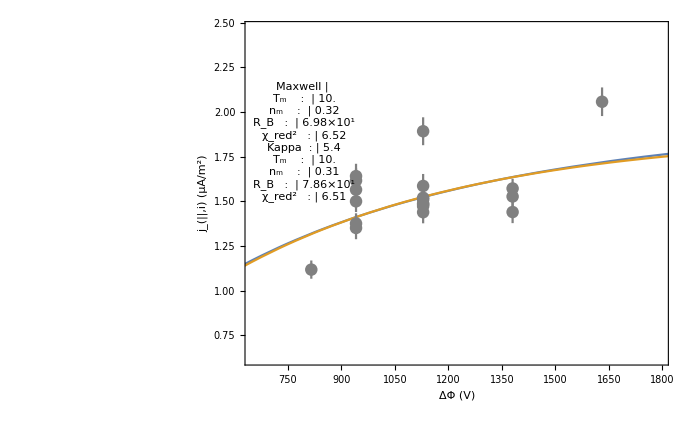

```mathematica
JVInitFitPlot=Show[Plot[{kInitialFit[pot],gInitialFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["Interval `1` (`2`)",interval,initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]
```

```mathematica
If[saveDataFiles,
DumpSave[initFitFile,{kInitialFit,gInitialFit,JVParTable,jErrData,initTitle,tid,jData,jErrData,jWt,potErr,curErr,potVal,curVal}];
Print["Saved "<>initFitFile];]
```

Saved /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180413/itvl2_kappa-fixT193eV-fixKappa2_6_nRolls5000_initialFits.wdx

#### Some Monte Carlo stuff for generating current uncertainty and potential uncertainty

```mathematica
genMCError:=RandomVariate[NormalDistribution[],nPots]*curErr[[currentInds]]
```

```mathematica
genPotVals:=potVal[[currentInds]]+RandomReal[{0,1},nPots]*potErr[[currentInds]]
```

```mathematica
inds=Range[1,nPots];
```

#### Visualize, Plot, See what synthetic data look like

```mathematica
currentInds=RandomChoice[inds,nPots];
```

```mathematica
curMCError=genMCError;
curPotVals=genPotVals;
```

```mathematica
curError=curErr[[currentInds]];
```

```mathematica
curjData=Partition[Riffle[curPotVals,((kInitialFit[#])&/@curPotVals)+curMCError],2];
```

```mathematica
curErrData=makeErrorData[curPotVals,curjData[[;;,2]],curError];
```

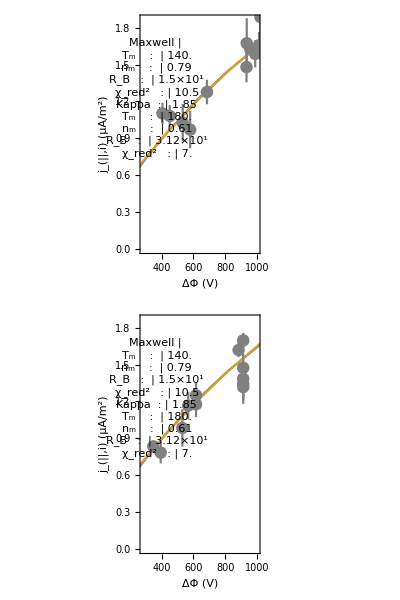

```mathematica
JVInitVsSynthPlot=Column[{Show[Plot[{kInitialFit[pot],gInitialFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[curErrData,PlotStyle->Gray]],Show[Plot[{kInitialFit[pot],gInitialFit[pot]},{pot,20,10000},PlotRange->{{minPot,maxPot},{minJ,maxJ}},Frame->True,FrameLabel->{{"j_(||,i) (μA/m^2)",""},{"ΔΦ (V)",Style[StringForm["J-V Fit (`1`)",initTitle],Bold,titleSize]}},ImageSize->700,FrameStyle->Directive[Black,axesLabelSize],Epilog->Inset[JVParTable,Scaled[{0.14,0.65}]]],ErrorListPlot[jErrData,PlotStyle->Gray]]}]
```

Do the Monte Carloing

```mathematica
countItvl=50;
currentInds=inds;
makePlots=True;
```

#### Some options

```mathematica
doBootstrap=False;
nTrials=5000;
saveDataFiles=True;
```

#### Kappa block

```mathematica
Block[{trials=nTrials, count=0,currentInds,curMCError,curPotVals,curjData,
kinitParams,kFitNinit,kFitTinit,kFitRBinit,kFitKappainit,kFit},
kMCStartupMessage;
kFitVals:=Flatten@Append[{Flatten@Append[{kFit["BestFitParameters"]},kFitValAdds]},kFitChi2red->Total[(kFit["FitResiduals"])^2*curWt]/kDOF];
If[doBootstrap==False,currentInds=inds;];
Monitor[kFits=Table[
(*If[Mod[count,countItvl]==0,Print[ToString@StringForm["Count: `1`",count]]];*)
If[doBootstrap,currentInds=RandomChoice[inds,nPots];];
curMCError=genMCError;
curError=curErr[[currentInds]];
curWt=1/curError^2;
curPotVals=genPotVals;
curjData=Partition[Riffle[curPotVals,((kInitialFit[#])&/@curPotVals)+curMCError],2];
kinitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax},{kappamin,kappamax}};
{kFitNinit,kFitTinit,kFitRBinit,kFitKappainit}=kinitParams;
kFit=NonlinearModelFit[curjData,(If[Length@kConstraints≠0,{kModel,kConstraints},kModel]),kFitVars,pot,Weights->curWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
count++;
(*{count, kFit["BestFitParameters"],kinitParams,kFit},trials];]*)
{count,Evaluate[ kFitOutput/.kFitVals],kinitParams,kFit},trials];,count]
];
```

Interval: 2

fixT    : 193

fixKappa: 2.6

```mathematica
If[saveDataFiles,DumpSave[(saveDir<>kDataFile),kFits];Print["Saved to "<>saveDir<>kDataFile]]
```

Saved to /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180413/Orb1612_itvl2_kappa-fixT193eV-fixKappa2_6_nRolls5000.wdx

#### Maxwell block

```mathematica
Block[{trials=nTrials, count=0,currentInds,curMCError,curPotVals,curjData,
ginitParams,gFitNinit,gFitTinit,gFitRBinit,gFit},
gMCStartupMessage;
gFitVals:=Flatten@Append[{Flatten@Append[{gFit["BestFitParameters"]},gFitValAdds]},gFitChi2red->Total[(gFit["FitResiduals"])^2*curWt]/gDOF];
If[doBootstrap==False,currentInds=inds;];
gFits=Monitor[Table[
If[doBootstrap,currentInds=RandomChoice[inds,nPots];];
curMCError=genMCError;
curError=curErr[[currentInds]];
curWt=1/curError^2;
curPotVals=genPotVals;
curjData=Partition[Riffle[curPotVals,((gInitialFit[#])&/@curPotVals)+curMCError],2];
ginitParams = RandomReal/@{{nmin,nmax},{Tmin,Tmax},{RBmin,RBmax}};
{gFitNinit,gFitTinit,gFitRBinit}=ginitParams;
gFit=NonlinearModelFit[curjData,(If[Length@gConstraints≠0,{gModel,gConstraints},gModel]),gFitVars,pot,Weights->curWt,VarianceEstimatorFunction->(1&),Method->fitMethod];
count++;
(*{count, kFit["BestFitParameters"],kinitParams,kFit},trials];]*)
{count,Evaluate[ gFitOutput/.gFitVals],ginitParams,gFit},trials],count];
];
```

Interval: 2

fixT    : 117

```mathematica
If[saveDataFiles,DumpSave [saveDir<>gDataFile,gFits];Print["Saved to "<>saveDir<>gDataFile]]
```

Saved to /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180413/Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000.wdx

Now check ‘em out

```mathematica
If[FileExistsQ[saveDir<>kDataFile],<<(saveDir<>kDataFile);
Print["Restored "<>saveDir<>kDataFile];
]
```

Restored /SPENCEdata/Research/Satellites/FAST/kappa_dists/saves_output_etc/20180413/Orb1612_itvl2_kappa-fixT198eV_nRolls5000.wdx

```mathematica
If[FileExistsQ[saveDir<>gDataFile],<<(saveDir<>gDataFile);
Print["Restored "<>saveDir<>gDataFile];
]
```

```mathematica
kMCVals=((kFits[[;;,2]])[[;;,#]])&/@{1,2,3,4};
```

```mathematica
gMCVals=((gFits[[;;,2]])[[;;,#]])&/@{1,2,3};
```

```mathematica
kMCTitles={"N (cm^-3)","T (eV)","R_B","κ"};
kMCPDFTitles={"PDF (cm^3)","PDF (eV^-1)","PDF (R_B^-1)","PDF (κ^-1)"};
gMCTitles={"N (cm^-3)","T (eV)","R_B"};
```

```mathematica
binSizes=Table[Automatic,4];
```

```mathematica
binSizes={{0.005},{0.2},{1},{0.2}};
```

```mathematica
MCTitle=StringJoin@Riffle[tid[[{1,-1}]],"–"];
```

```mathematica
densPlotRange:=Switch[interval,1,{{0,75},{0.3,0.6}},2,{{0,80},{0.4,1.2}}];
```

## Kappa plots

#### Itvl 1, fixT=133 eV, nRoll= 5000

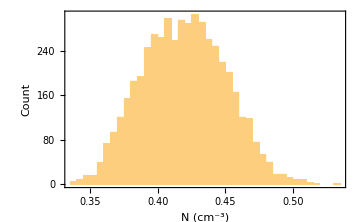
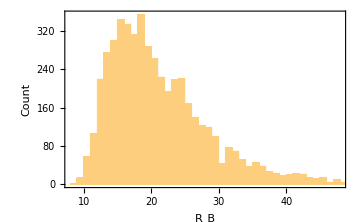
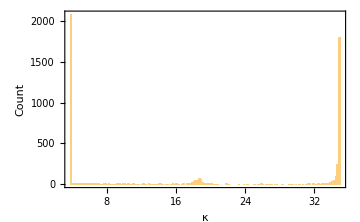
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

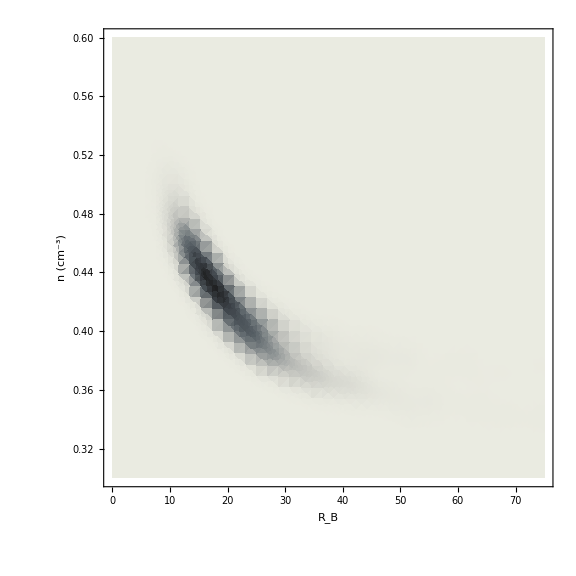

```mathematica
SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

#### Itvl 1, fixT=124 eV, nRoll= 5000

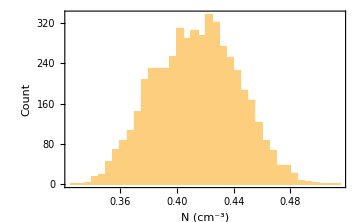
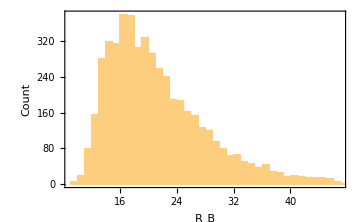
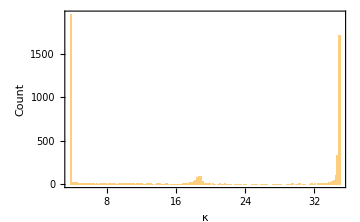
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

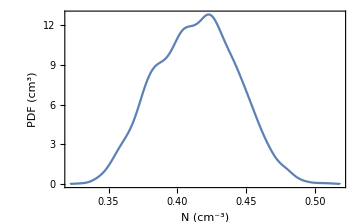
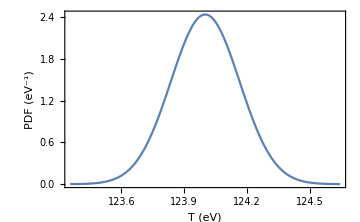
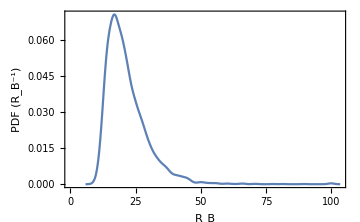
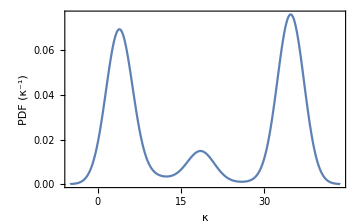

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[kMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

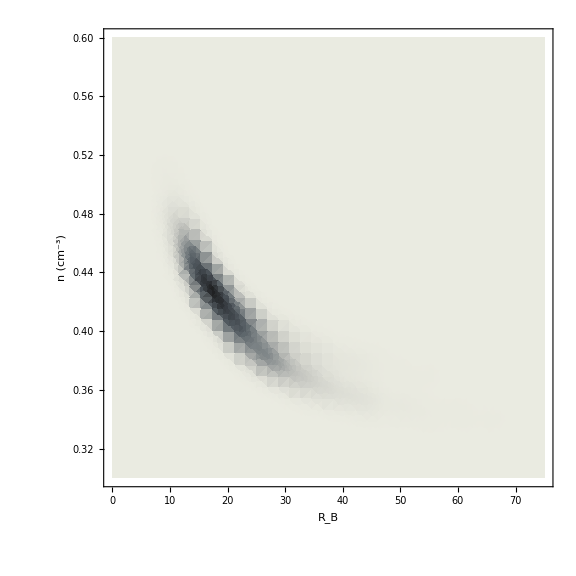

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[kDensityHistoFile<>" ..."];
Export[plotDir<>kDensityHistoFile,kDensityHisto];
Print[kHistosPlotFile<>" ..."];
Export[plotDir<>kHistosPlotFile,kHistosPlot];
Print[kSmoothHistosPlotFile<>" ..."];
Export[plotDir<>kSmoothHistosPlotFile,kSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl1_kappa-fixT124eV_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl1_kappa-fixT124eV_nRolls5000__histograms.pdf ...

Orb1612_itvl1_Maxwell-fixT140eV_nRolls5000__smoothHistograms.pdf ...

Done!

#### Itvl 2, fixT=193 eV, nRoll= 5000

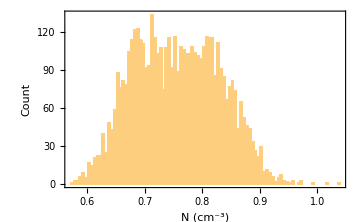
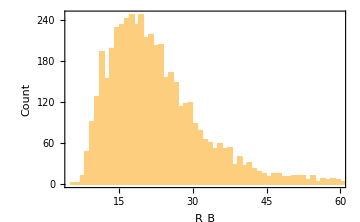
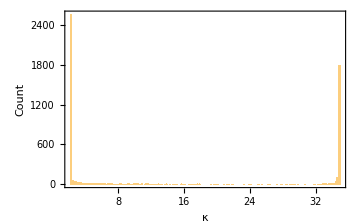
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

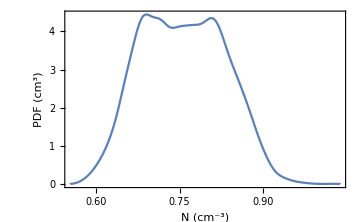
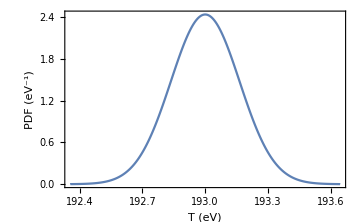
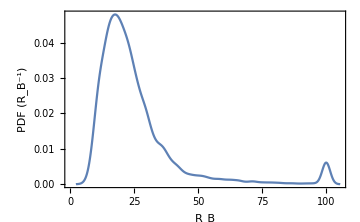
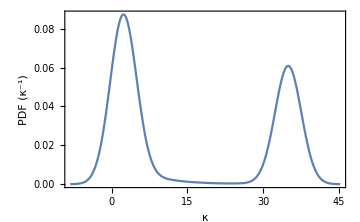

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[kMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

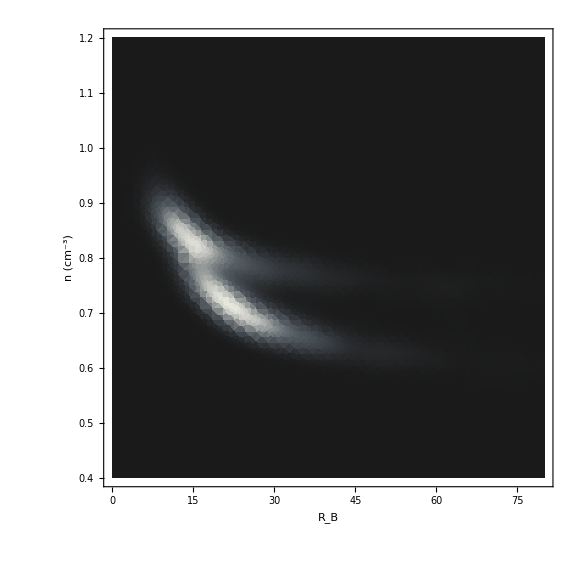

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData["GrayTones"]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[kDensityHistoFile<>" ..."];
Export[plotDir<>kDensityHistoFile,kDensityHisto];
Print[kHistosPlotFile<>" ..."];
Export[plotDir<>kHistosPlotFile,kHistosPlot];
Print[kSmoothHistosPlotFile<>" ..."];
Export[plotDir<>kSmoothHistosPlotFile,kSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl2_kappa-fixT193eV_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl2_kappa-fixT193eV_nRolls5000__histograms.pdf ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__smoothHistograms.pdf ...

Done!

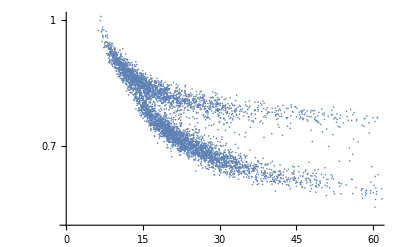

```mathematica
ListLogPlot[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2]]
```

#### Itvl 2, fixT=193 eV, fixKappa=2.6, nRoll= 5000

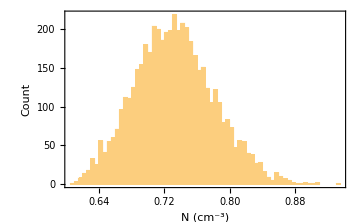
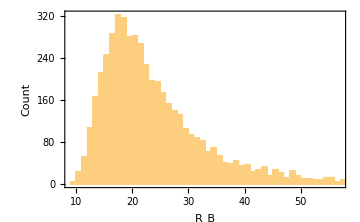
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kHistosPlot=Row[Table[Histogram[kMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],"Count"},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

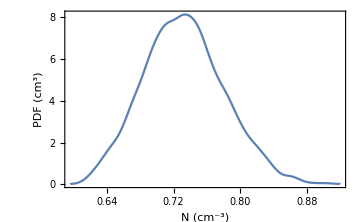
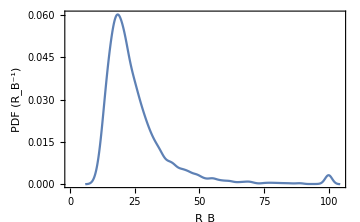
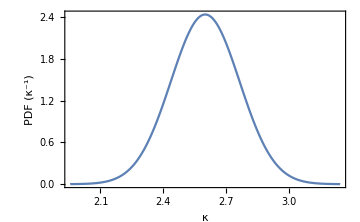
-Graphics--Graphics--Graphics--Graphics-

```mathematica
kSmoothHistosPlot=Row[Table[SmoothHistogram[kMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3,4}}]]
```

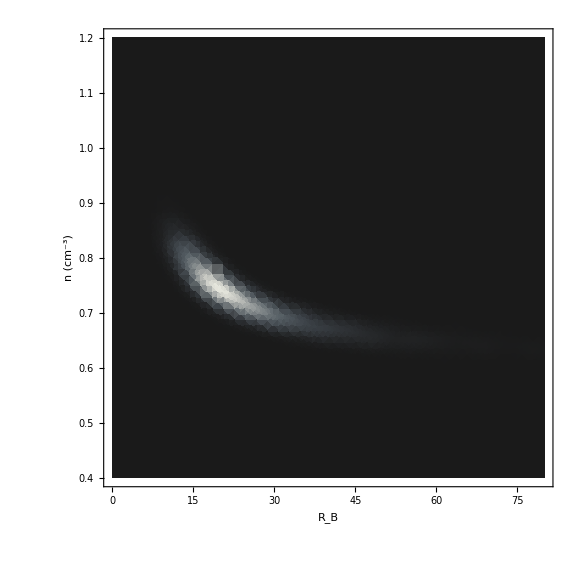

```mathematica
kDensityHisto=SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData["GrayTones"]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[kDensityHistoFile<>" ..."];
Export[plotDir<>kDensityHistoFile,kDensityHisto];
Print[kHistosPlotFile<>" ..."];
Export[plotDir<>kHistosPlotFile,kHistosPlot];
Print[kSmoothHistosPlotFile<>" ..."];
Export[plotDir<>kSmoothHistosPlotFile,kSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl2_kappa-fixT193eV-fixKappa2_6_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl2_kappa-fixT193eV-fixKappa2_6_nRolls5000__histograms.pdf ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__smoothHistograms.pdf ...

Done!

```mathematica
ListLogPlot[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2]]
```

-Graphics-

#### Itvl 2, fixT=198 eV, nRoll= 5000

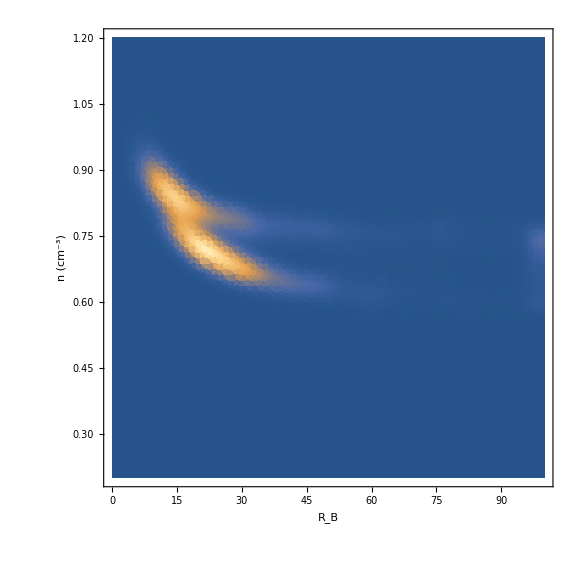

```mathematica
SmoothDensityHistogram[Partition[Riffle[kMCVals[[3]],kMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Kappa, N = `2`)",MCTitle,nTrials],Bold,20]}}]
```

## Maxwellian plots

#### Itvl 1, fixT=120 eV, nRoll= 5000

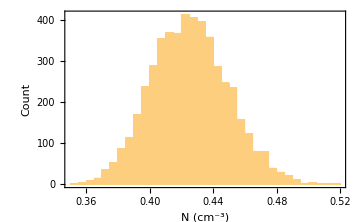
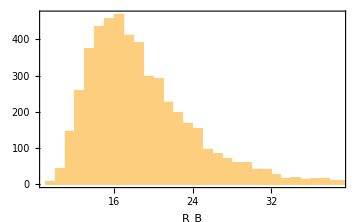
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

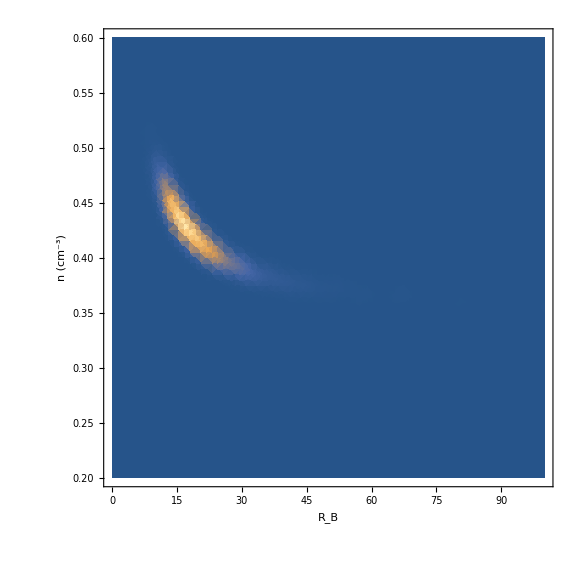

```mathematica
SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}}]
```

#### Itvl 1, fixT=133 eV, nRoll= 5000

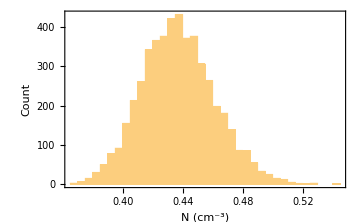
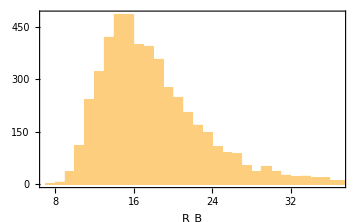
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

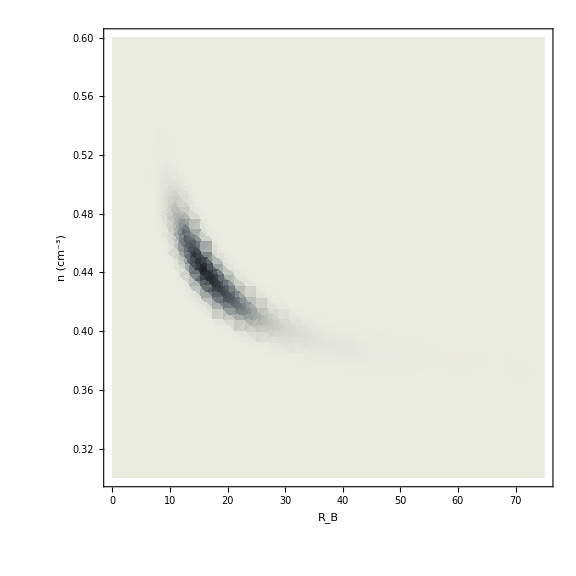

```mathematica
SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

#### Itvl 1, fixT=140 eV, nRoll= 5000

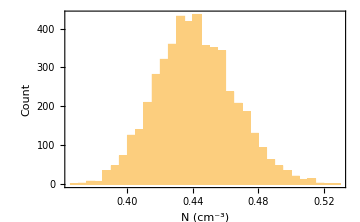
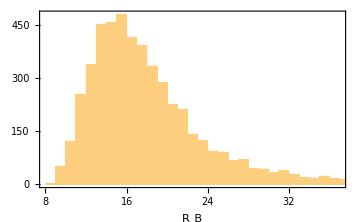
-Graphics--Graphics--Graphics-

```mathematica
gHistosPlot=Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

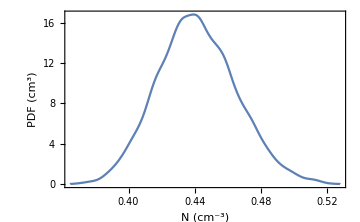
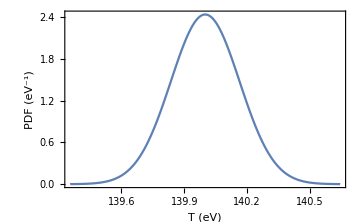
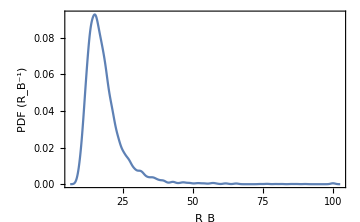

```mathematica
gSmoothHistosPlot=Row[Table[SmoothHistogram[gMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,PlotRange->Full,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

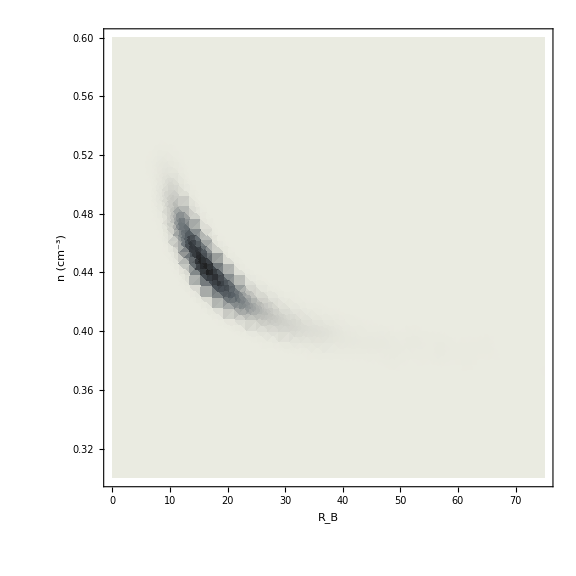

```mathematica
gDensityHisto=SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[gDensityHistoFile<>" ..."];
Export[plotDir<>gDensityHistoFile,gDensityHisto];
Print[gHistosPlotFile<>" ..."];
Export[plotDir<>gHistosPlotFile,gHistosPlot];
Print[gSmoothHistosPlotFile<>" ..."];
Export[plotDir<>gSmoothHistosPlotFile,gSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl1_Maxwell-fixT140eV_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl1_Maxwell-fixT140eV_nRolls5000__histograms.pdf ...

Orb1612_itvl1_Maxwell-fixT140eV_nRolls5000__smoothHistograms.pdf ...

Done!

#### Itvl 2, fixT=140 eV, nRoll= 5000

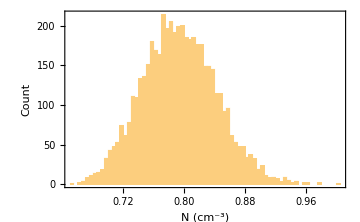
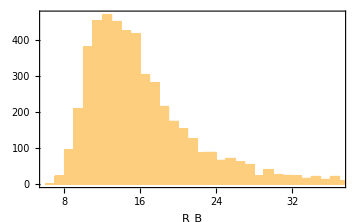
-Graphics--Graphics--Graphics-

```mathematica
Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

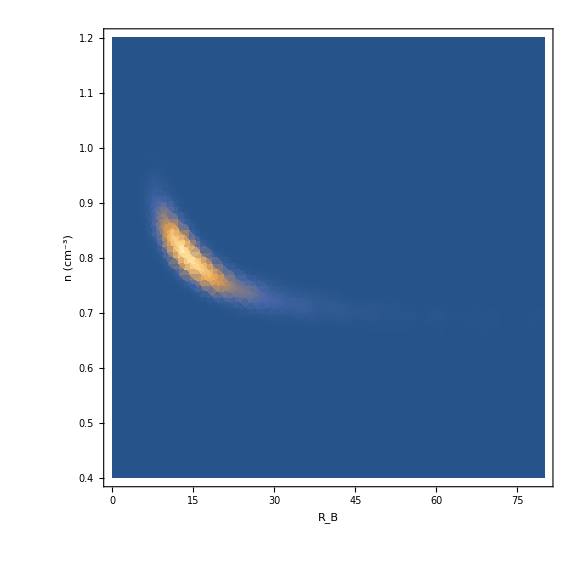

```mathematica
SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->{{0,80},{0.4,1.2}},Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}}]
```

#### Itvl 2, fixT=117 eV, nRoll= 5000

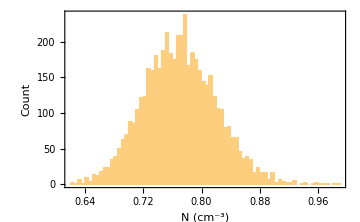
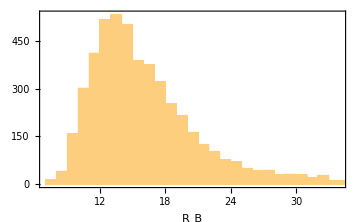
-Graphics--Graphics--Graphics-

```mathematica
gHistosPlot=Row[Table[Histogram[gMCVals[[MCParmInd]],binSizes[[MCParmInd]],ImageSize->Medium,Frame->True,FrameLabel->{gMCTitles[[MCParmInd]],If[MCParmInd==1,"Count",""]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

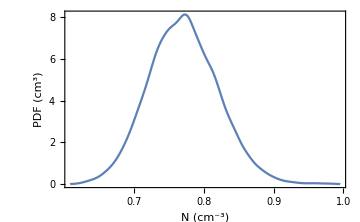
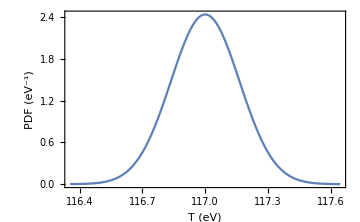
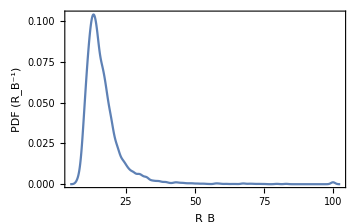

```mathematica
gSmoothHistosPlot=Row[Table[SmoothHistogram[gMCVals[[MCParmInd]],ImageSize->Medium,Frame->True,PlotRange->Full,FrameLabel->{kMCTitles[[MCParmInd]],kMCPDFTitles[[MCParmInd]]},FrameStyle->Directive[FontSize->16]],{MCParmInd,{1,2,3}}]]
```

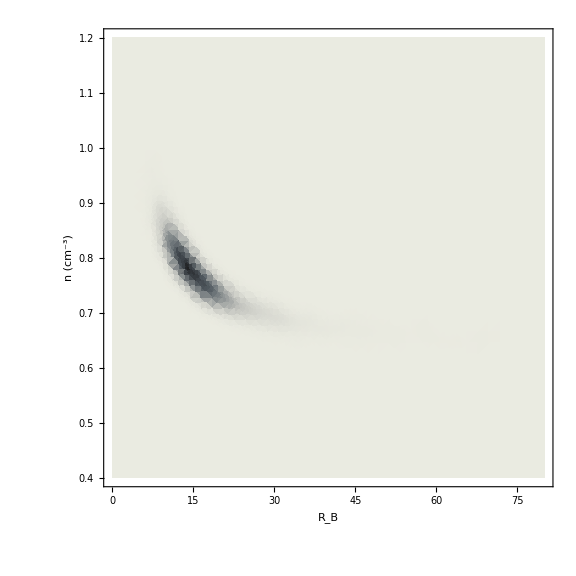

```mathematica
gDensityHisto=SmoothDensityHistogram[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,PlotRange->densPlotRange,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,nTrials],Bold,20]}},
ColorFunction->ColorData[{"GrayTones","Reverse"}]]
```

```mathematica
If[makePlots,Print["Making plots in "<>dir<>" ..."];
Print[gDensityHistoFile<>" ..."];
Export[plotDir<>gDensityHistoFile,gDensityHisto];
Print[gHistosPlotFile<>" ..."];
Export[plotDir<>gHistosPlotFile,gHistosPlot];
Print[gSmoothHistosPlotFile<>" ..."];
Export[plotDir<>gSmoothHistosPlotFile,gSmoothHistosPlot];
Print["Done!"]]
```

Making plots in /SPENCEdata/Research/Satellites/FAST/kappa_dists/journals/ ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__smoothDensityHistogram.pdf ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__histograms.pdf ...

Orb1612_itvl2_Maxwell-fixT117eV_nRolls5000__smoothHistograms.pdf ...

Done!

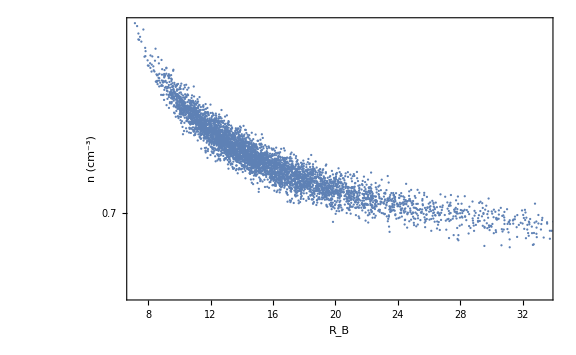

```mathematica
ListLogPlot[Partition[Riffle[gMCVals[[3]],gMCVals[[1]]],2],ImageSize->Large,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"n (cm^-3)",""},{"R_B",Style[ToString@StringForm["`1` (Maxwellian, N = `2`)",MCTitle,1000],Bold,20]}}]
```

#### Some Maxwellian/kappa combo histos

```mathematica
plotLegs=If[doFixT,
{StringForm["Maxwellian (T = `1` eV)",gfixTVal],StringForm["Kappa ∈ [`1`,`2`] (T = `3` eV)",minFitKappa,maxFitKappa,kfixTVal]},{"Maxwellian",StringForm["Kappa ∈ [`1`,`2`]",minFitKappa,maxFitKappa]}
]
```

{Maxwellian (T = 117 eV),Kappa ∈ [2.24,35] (T = 193 eV)}

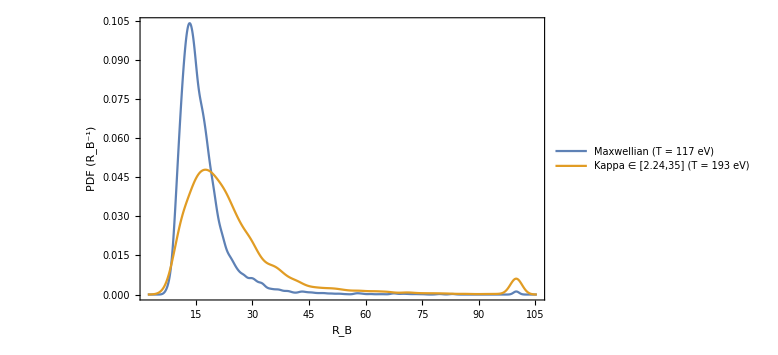

```mathematica
SmoothHistogram[{gMCVals[[3]],kMCVals[[3]]},PlotLegends->plotLegs,ImageSize->Large,PlotRange->Full,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"PDF (R_B^-1)",""},{"R_B",Style[ToString@StringForm["`1` (N = `2`)",MCTitle,nTrials],Bold,20]}}]
```

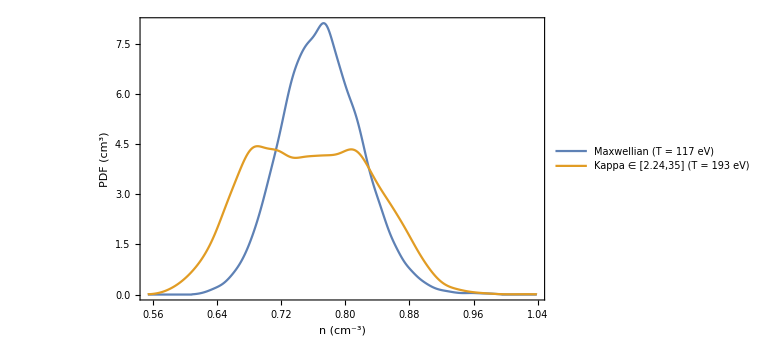

```mathematica
SmoothHistogram[{gMCVals[[1]],kMCVals[[1]]},PlotLegends->plotLegs,ImageSize->Large,PlotRange->Full,Frame->True,FrameStyle->FontSize->16, FrameLabel->{{"PDF (cm^3)",""},{"n (cm^-3)",Style[ToString@StringForm["`1` (N = `2`)",MCTitle,nTrials],Bold,20]}}]
```